```mathematica
b = {2,-8};
x = {3*x1 + 2*x2,2*x1 + 6 *x2};
b.x
```

2 (3 x1+2 x2)-8 (2 x1+6 x2)

-2 x1+8 x2+0.5 (x1 (3 x1+2 x2)+x2 (2 x1+6 x2))

-Graphics3D-

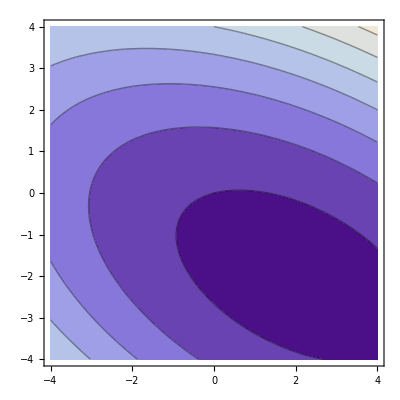

Part::partw: Part 1 of {} does not exist.

-Graphics-

```mathematica
A = {{3,2},{2,6}};
b = {2,-8};
x = {x1,x2};

Cs =0.5*x.A.x - b.x
Plot3D[Cs, {x1, -4,4},{x2,-4,4}]
ContourPlot[Cs, {x1, -4,4},{x2,-4,4}]
VectorPlot[Cs, {x1, -4,4},{x2,-4,4}]
```

```mathematica
{{-2 x1+1.5 x1^2,-2 x1+1. x1^2},{8 x2+1. x2^2,8 x2+3. x2^2}}
```

```mathematica
b1 = {1,2};
b2 = {3,4};
b1*b2
```

{3,8}

```mathematica
b2*b1
```

{3,8}